# Introduction to Linear Algebra

## Matrices and Matrix Operations

A 2 x 3 matrix:

```mathematica
A={{4, 2, -3}, {11, π, 12}};
```

A 4 x 1 matrix:

```mathematica
B = {{1}, {34}, {-12}, {0}};
```

A gray scale image defined using a matrix of pixel brightness values

```mathematica
Image[({{0.1, 0.9, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})]
```

-Graphics-

A colored image defined using a matrix of rgb brightness values

```mathematica
Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}}), ColorSpace -> "RGB"]
```

-Graphics-

```mathematica
A[[2,3]]
```

12

## Matrix Arithmetic

Matrix Addition

```mathematica
({{_a11, _a12, _a13, _a14}, {_a21, _a22, _a23, _a24}, {_a31, _a32, _a33, _a34}})+({{_b11, _b12, _b13, _b14}, {_b21, _b22, _b23, _b24}, {_b31, _b32, _b33, _b34}})//MatrixForm
({{2, 3, 4, -1}, {-2, 0, 2, 2}, {1, 2, -1, 0}})+({{-1, 2, 2, -2}, {-3, 0, 1, 0}, {0, 0, -2, 1}})//MatrixForm
```

(_a11+_b11 | _a12+_b12 | _a13+_b13 | _a14+_b14
_a21+_b21 | _a22+_b22 | _a23+_b23 | _a24+_b24
_a31+_b31 | _a32+_b32 | _a33+_b33 | _a34+_b34)

(1 | 5 | 6 | -3
-5 | 0 | 3 | 2
1 | 2 | -3 | 1)

Matrix Multiplication

```mathematica
({{_a11, _a12, _a13}, {_a21, _a22, _a23}}).({{_b11, _b12}, {_b21, _b22}, {_b31, _b32}})//MatrixForm
({{2, 1, -3}, {-1, 0, 1}}).({{2, 1}, {-1, 3}, {3, 1}})//MatrixForm
```

(_a11 _b11+_a12 _b21+_a13 _b31 | _a11 _b12+_a12 _b22+_a13 _b32
_a21 _b11+_a22 _b21+_a23 _b31 | _a21 _b12+_a22 _b22+_a23 _b32)

(-6 | 2
1 | 0)

Identity Matrix

```mathematica
Identity2 = ({{1, 0}, {0, 1}});
Identity3 = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
Identity4 = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
({{_a11, _a12, _a13}, {_a21, _a22, _a23}}).Identity3//MatrixForm
({{2, 1, -3}, {-1, 0, 1}}).Identity3//MatrixForm
```

(_a11 | _a12 | _a13
_a21 | _a22 | _a23)

(2 | 1 | -3
-1 | 0 | 1)

```mathematica
({{1, 5, 6, -3}, {-5, 0, 3, 2}, {1, 2, -3, 1}}).Identity4//MatrixForm
```

(1 | 5 | 6 | -3
-5 | 0 | 3 | 2
1 | 2 | -3 | 1)

Transpose of a Matrix

```mathematica
Transpose[({{1, 5, 6, -3}, {-5, 0, 3, 2}, {1, 2, -3, 1}})]//MatrixForm
Transpose[({{2, 1, -3}, {-1, 0, 1}})]//MatrixForm
```

(1 | -5 | 1
5 | 0 | 2
6 | 3 | -3
-3 | 2 | 1)

(2 | -1
1 | 0
-3 | 1)

False Identity Matrix

```mathematica
({{1, -5, 1}, {5, 0, 2}, {6, 3, -3}, {-3, 2, 1}}).({{0, 0, 1}, {0, 1, 0}, {1, 0, 0}})//MatrixForm
({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}).({{1, -5, 1}, {5, 0, 2}, {6, 3, -3}, {-3, 2, 1}})//MatrixForm
```

(1 | -5 | 1
2 | 0 | 5
-3 | 3 | 6
1 | 2 | -3)

(-3 | 2 | 1
6 | 3 | -3
5 | 0 | 2
1 | -5 | 1)

## Linear Algebra

Vector Addition

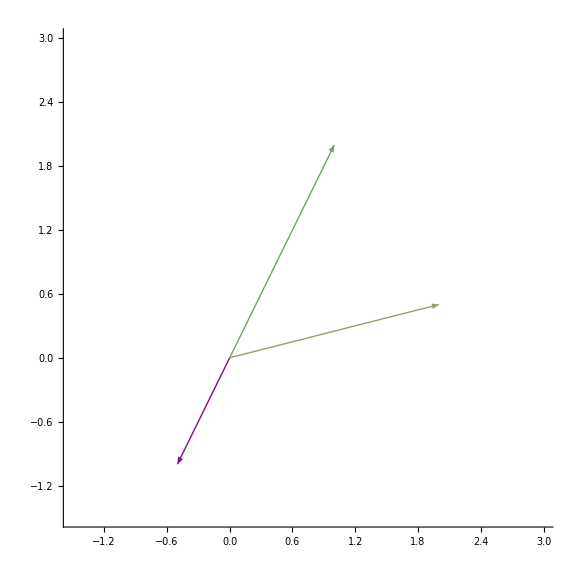

```mathematica
origin = {0,0};
MakeArrow[v_]:=Arrow[{origin,v}]
MakeTArrow[v_]:={Opacity[0.2],MakeArrow[v]}
MakeT2Arrow[v_]:={Opacity[0.5],Red,MakeArrow[v]}
MakeColorArrow[c_,v_]:={c,Thick,MakeArrow[v]}
AutoColorArrow[v_]:={RGBColor[(v[[1]]+5)/10,0,(v[[2]]+5)/10],MakeArrow[v]}
MakePoint[v_]:={PointSize[Large],Point[v]}
MakeGrid[v_]:={{Line[{{v[[1]],-10},{v[[1]],10}}]},{Line[{{-10,v[[2]]},{10,v[[2]]}}]}}
v1 = ({{-0.5}, {-1}});
v2=({{1}, {2}});
v3 = ({{2}, {0.5}});
T[v_]:=Flatten[Transpose[v]]
RenderVectors[vlist_,plotrange_:{{-3,3},{-3,3}}]:=Graphics[Map[MakeColorArrow[RGBColor[RandomReal[{0,0.7}],RandomReal[{0,0.7}],RandomReal[{0,0.7}]],T[#]]&,vlist],Axes->{True,True},PlotRange->plotrange]
Show[RenderVectors[{v1,v2,v3},{{-1.5,3},{-1.5,3}}],ImageSize-> Large]
```

```mathematica
origin3d={0,0,0};
Make3dArrow[v_]:=Arrow[Tube[{origin3d,v}]]
Make3dColorArrow[c_,v_]:={Opacity[0.5],c,Thick,Make3dArrow[v]}
Make3dPoint[v_]:={PointSize[Large],Point[v]}
RenderVectors3d[vlist_,plotrange_:{{-3,3},{-3,3},{-3,3}}]:=Graphics3D[Map[Make3dColorArrow[RGBColor[RandomReal[{0,0.7}],RandomReal[{0,0.7}],RandomReal[{0,0.7}]],T[#]]&,vlist],Axes->{True,True},PlotRange->plotrange,AxesOrigin->{0,0,0},Boxed->False]
Show[RenderVectors3d[{({{1}, {2}, {-1}}),({{2}, {-1}, {0}}),({{-1}, {0}, {-1}})},{{-2,2},{-2,2},{-2,1}}],ImageSize-> Large]
```

-Graphics3D-

```mathematica
redRGB=RGBColor[{1,0,0}];
blueRGB=RGBColor[{0,0,1}];
greenRGB=RGBColor[{0,1,0}];

ColorAdd[c1_,c2_]:=RGBColor[{(c1[[1]][[1]]+c2[[1]][[1]])/2,(c1[[1]][[2]]+c2[[1]][[2]])/2,(c1[[1]][[3]]+c2[[1]][[3]])/2}]
VectorAddRender[v1_,v2_,plotrange_:Automatic]:=Graphics[{MakeColorArrow[redRGB,T[v1]],MakeColorArrow[blueRGB,T[v2]],MakeColorArrow[ColorAdd[redRGB,blueRGB],T[v1]+T[v2]],{blueRGB,Dashed,Arrow[{T[v1],T[v1]+T[v2]}]},{redRGB,Dashed,Arrow[{T[v2],T[v1]+T[v2]}]}},Axes->{True,True},PlotRange->plotrange]
Show[VectorAddRender[({{3}, {0.5}}),({{0.5}, {-2}}),{{-0.5,4},{-2.5,1}}],ImageSize-> Large]
```

-Graphics-

```mathematica
VectorAddRender3d[v1_,v2_,plotrange_:Automatic]:=Graphics3D[{Make3dColorArrow[redRGB,T[v1]],Make3dColorArrow[blueRGB,T[v2]],Make3dColorArrow[ColorAdd[redRGB,blueRGB],T[v1]+T[v2]],{blueRGB,Dashed,Arrow[{T[v1],T[v1]+T[v2]}]},{redRGB,Dashed,Arrow[{T[v2],T[v1]+T[v2]}]}},Axes->{True,True,True},AxesOrigin->origin3d,Boxed->False]
Show[VectorAddRender3d[({{1}, {3}, {1}}),({{-2}, {1}, {-3}})],ImageSize-> Large]
```

-Graphics3D-

Vector Multiplication

```mathematica
RenderVectors3dRed[vlist_,plotrange_:{{-3,3},{-3,3},{-3,3}}]:=Graphics3D[Map[Make3dColorArrow[Red,T[#]]&,vlist],Axes->{True,True},PlotRange->plotrange,AxesOrigin->{0,0,0},Boxed->False]
```

```mathematica
Manipulate[Show[RenderVectors3dRed[{i({{3}, {0.5}, {0}})},{{-6,6},{-6,6},{-2,6}}],ImageSize-> Large],{{i,1,"scalar"},-2,4},SaveDefinitions->True]
```

```mathematica
RenderVectorsRed[vlist_,plotrange_:{{-3,3},{-3,3}}]:=Graphics[Map[MakeColorArrow[Red,T[#]]&,vlist],Axes->{True,True},PlotRange->plotrange]
```

```mathematica
Manipulate[Show[RenderVectorsRed[{i({{3}, {0.5}})},{{-6,6},{-2,2}}],ImageSize-> Large],{{i,1,"scalar"},-2,4},SaveDefinitions->True]
```

Basis Vectors

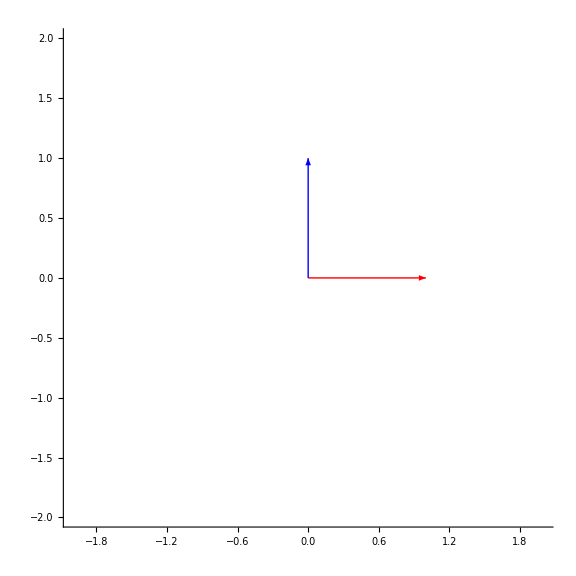

```mathematica
BasisRender[v1_,v2_,plotrange_:Automatic]:=Graphics[{MakeColorArrow[redRGB,T[v1]],MakeColorArrow[blueRGB,T[v2]]},Axes->{True,True},PlotRange->plotrange]
Show[BasisRender[({{1}, {0}}),({{0}, {1}}),{{-2,2},{-2,2}}],ImageSize-> Large]
```

```mathematica
BasisRender3d[v1_,v2_,v3_,plotrange_:Automatic]:=Graphics3D[{Make3dColorArrow[Red,T[v1]],Make3dColorArrow[Blue,T[v2]],Make3dColorArrow[Green,T[v3]]},Axes->{True,True},PlotRange->plotrange,AxesOrigin->{0,0,0},Boxed-> False]
Show[BasisRender3d[({{1}, {0}, {0}}),({{0}, {1}, {0}}),({{0}, {0}, {1}}),{{-2,2},{-2,2},{-2,2}}],ImageSize-> Large]
```

-Graphics3D-

Forming any Vector from Basis Vector

```mathematica
Manipulate[VectorAddRender[a({{1}, {0}}),b({{0}, {1}}),{{-3,3},{-3,3}}],{{a,1,"ihat coef"},-3,3},{{b,1,"jhat coef"},-3,3},SaveDefinitions->True]
```

```mathematica
VectorTripleAddRender3d[v1_,v2_,v3_,plotrange_:Automatic]:=Graphics3D[{Make3dColorArrow[redRGB,T[v1]],Make3dColorArrow[blueRGB,T[v2]],Make3dColorArrow[greenRGB,T[v3]],Make3dColorArrow[Black,T[v1]+T[v2]+T[v3]],{redRGB,Dashed,Thick,Line[{T[v2]+T[v3],T[v1]+T[v2]+T[v3]}]},{redRGB,Dashed,Thick,Line[{T[v2],T[v1]+T[v2]}]},{redRGB,Dashed,Thick,Line[{T[v3],T[v1]+T[v3]}]},{blueRGB,Dashed,Thick,Line[{T[v1],T[v1]+T[v2]}]},{blueRGB,Dashed,Thick,Line[{T[v1]+T[v3],T[v1]+T[v2]+T[v3]}]},{blueRGB,Dashed,Thick,Line[{T[v3],T[v2]+T[v3]}]},{greenRGB,Dashed,Thick,Line[{T[v1]+T[v2],T[v1]+T[v2]+T[v3]}]},{greenRGB,Dashed,Thick,Line[{T[v1],T[v1]+T[v3]}]},{greenRGB,Dashed,Thick,Line[{T[v2],T[v2]+T[v3]}]}},Axes->{True,True,True},AxesOrigin->origin3d,Boxed->False,PlotRange->plotrange]
```

```mathematica
Manipulate[Show[VectorTripleAddRender3d[a({{1}, {0}, {0}}),b({{0}, {1}, {0}}),c({{0}, {0}, {1}}),{{-2,2},{-2,2},{-2,2}}],ImageSize-> Large],{{a,1,"ihat coef"},-3,3},{{b,1,"jhat coef"},-3,3},{{c,1,"khat coef"},-3,3},SaveDefinitions->True]
```

```mathematica
MakeSpan[v1_,v2_,spacing_:1]:=Flatten[Table[i v1+j v2,{i,-5,5,spacing},{j,-5,5,spacing}],1]
RenderSpan[v1_,v2_,plotrange_:Automatic]:=Graphics[Join[Map[MakeArrow,MakeSpan[T[v1],T[v2]]],{{RGBColor[1,0,0],Thick,Arrow[{origin,T[v1]}]},{Blue,Thick,Arrow[{origin,T[v2]}]}}],Axes->{True,True},PlotRange->plotrange]
```

```mathematica
Manipulate[Show[RenderSpan[({{a}, {c}}),({{b}, {d}}),{{-4,4},{-4,4}}],ImageSize-> Large],{{a,1,"a"},-3,3},{{b,0,"b"},-3,3},{{c,0,"c"},-3,3},{{d,1,"d"},-3,3},SaveDefinitions->True]
```

```mathematica
Make3dSpan[v1_,v2_,v3_,spacing_:3]:=Flatten[Table[i v1+j v2+k v3,{i,-5,5,spacing},{j,-5,5,spacing},{k,-5,5,spacing}],2]
Render3dSpan[v1_,v2_,v3_,plotrange_:{{-5,5},{-5,5},{-5,5}}]:=Graphics3D[Join[{Opacity[0.4],Map[Make3dArrow,Make3dSpan[T[v1],T[v2],T[v3]]]},{{Opacity[1],Red,Thick,Arrow[Tube[{origin3d,T[v1]}]]},{Opacity[1],Blue,Thick,Arrow[Tube[{origin3d,T[v2]}]]},{Opacity[1],Green,Thick,Arrow[Tube[{origin3d,T[v3]}]]}}],Axes->{True,True,True},Boxed->True,AxesOrigin->origin3d,PlotRange->plotrange]
```

```mathematica
Manipulate[Show[Render3dSpan[({{a}, {d}, {g}}),({{b}, {e}, {h}}),({{c}, {f}, {i}})],ImageSize-> Large],{{a,1},-3,3},{{b,0},-3,3},{{c,0},-3,3},{{d,0},-3,3},{{e,1},-3,3},{{f,0},-3,3},{{g,0},-3,3},{{h,0},-3,3},{{i,1},-3,3},SaveDefinitions->True]
```

```mathematica
Show[Render3dSpan[({{1}, {0}, {0}}),({{0}, {1}, {0}}),({{0}, {0}, {1}})],ImageSize-> Large]
```

-Graphics3D-

## Linear Transformations

```mathematica
identity={{1,0},{0,1}};
rotate90={{0,-1},{1,0}};
hflip={{1,0},{0,-1}};
stretchx={{2,0},{0,1}};
shrinkx={{0.5,0},{0,1}};
stretchy={{1,0},{0,2}};
stretchxy={{2,0},{0,2}};
sheary={{1,0},{1,1}};
shearx={{1,1},{0,1}};
shrink={{0,1},{0,2}};
MakeTGrid[t_,v_]:={{Opacity[0.01],Thin,Line[{t.{v[[1]],-10},t.{v[[1]],10}}]},{Opacity[0.01],Thin,Line[{t.{-10,v[[2]]},t.{10,v[[2]]}}]}}
MakeTGrid3d[t_,v_]:={{Opacity[0.5],Thin,Line[{t.{v[[1]],v[[2]],-10},t.{v[[1]],v[[2]],10}}]},{Opacity[0.5],Thin,Line[{t.{-10,v[[2]],v[[3]]},t.{10,v[[2]],v[[3]]}}]},{Opacity[0.5],Thin,Line[{t.{v[[1]],-10,v[[3]]},t.{v[[1]],10,v[[3]]}}]}}
GridTransform[t_,b1_,b2_,vlist_,colors_,plotrange_:{{-5,5},{-5,5}}]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->plotrange]
GridTransform3d[t_,b1_,b2_,b3_,vlist_,colors_,plotrange_:{{-3,3},{-3,3},{-3,3}}]:=Graphics3D[Join[Map[MakeTGrid3d[t,#]&,Make3dSpan[b1,b2,b3]],{Make3dColorArrow[Red,t.b1],Make3dColorArrow[Blue,t.b2],Make3dColorArrow[Green,t.b3]},MapThread[Make3dColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True,True},PlotRange->plotrange]
```

```mathematica
Manipulate[Show[GridTransform[identity-0.02i(identity-({{0, 1}, {-1, 0}})),{1,0},{0,1},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black},{{-4,4},{-4,4}}],ImageSize-> Large],{i,0,50},SaveDefinitions->True]
```

```mathematica
b1={1,0,0};
b2={0,1,0};
b3={0,0,1};
```

```mathematica
Manipulate[Show[GridTransform3d[Identity3-0.02i(Identity3-({{1, 0, 1}, {0, 1, 0}, {1, 0, 1}})),b1,b2,b3,{{2,0,1}},{Brown},{{-6,6},{-6,6},{-6,6}}],ImageSize-> Large],{i,0,50},SaveDefinitions->True]
```

The cell below might be un- evaluatable remember to set it as evaluatable if you want to re-export the animation frames

```mathematica
MapThread[Export[NotebookDirectory[]<>"/rotate90/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-({{0, 1}, {-1, 0}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
MapThread[Export[NotebookDirectory[]<>"/stretchx/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-({{2, 0}, {0, 1}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
MapThread[Export[NotebookDirectory[]<>"/stretchy/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,
{Table[Show[GridTransform[identity-0.02i(identity-({{1, 0}, {0, 2}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
MapThread[Export[NotebookDirectory[]<>"/shearx/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-({{1, 1}, {0, 1}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
MapThread[Export[NotebookDirectory[]<>"/sheary/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-({{1, 0}, {1, 1}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
MapThread[Export[NotebookDirectory[]<>"/flipx/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-({{1, 0}, {0, -1}})),{0,1},{1,0},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
```

```mathematica
Manipulate[Show[GridTransform[(identity-0.02j(identity-({{1, 1}, {0, 1}}))).(identity-0.02i(identity-({{0, -1}, {1, 0}}))),{1,0},{0,1},{{1,1},{2,1},{-2,0.5},{1,-2}},{Green, Brown,Yellow,Black},{{-4,4},{-4,4}}],ImageSize-> Large],{i,0,50},{j,0,50},SaveDefinitions->True]
```

```mathematica
GridTransformDeterminant[t_,b1_,b2_,plotrange_:{{-3,3},{-3,3}}]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[T[b1],T[b2]]],{MakeColorArrow[Red,t.T[b1]],MakeColorArrow[Blue,t.T[b2]]},{Yellow,Opacity[0.5],Polygon[{t.{0,0},t.T[b2],t.T[b1+b2],t.T[b1]}]}],Axes-> {True,True},PlotRange->plotrange]
```

Determinant

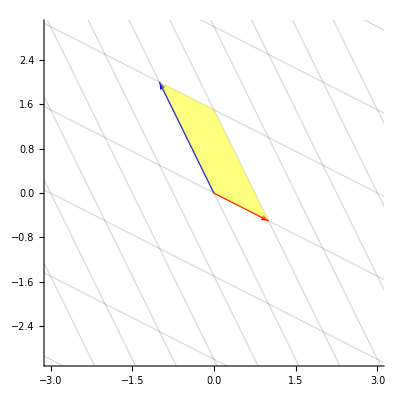

```mathematica
GridTransformDeterminant[({{1, -1}, {-0.5, 2}}),({{1}, {0}}),({{0}, {1}})]
```

```mathematica
Manipulate[Show[GridTransformDeterminant[identity-0.02i(identity-({{1, -1}, {-0.5, 2}})),({{1}, {0}}),({{0}, {1}})],ImageSize-> Large],{i,0,50},SaveDefinitions->True]
```

```mathematica
GridTransform3dDet[t_,b1_,b2_,b3_,plotrange_: {{-5,5},{-5,5},{-5,5}}]:=Graphics3D[Join[{Make3dColorArrow[Red,t.T[b1]],Make3dColorArrow[Blue,t.T[b2]],Make3dColorArrow[Green,t.T[b3]]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b1],t.T[b1+b2],t.T[b2]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b3],t.T[b1+b3],t.T[b1+b2+b3],t.T[b2+b3]}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b3],t.T[b1+b3],t.T[b1]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b2],t.T[b2+b3],t.T[b1+b2+b3],t.T[b1+b2]}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b3],t.T[b2+b3],t.T[b2]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b1],t.T[b1+b3],t.T[b1+b2+b3],t.T[b1+b2]}]}],Axes->{True,True,True},PlotRange->plotrange]
```

```mathematica
Manipulate[Show[GridTransform3dDet[Identity3-0.02i(Identity3-({{1, -1, 2}, {0, 2, -1}, {1, 2, -2}})),({{1}, {0}, {0}}),({{0}, {1}, {0}}),({{0}, {0}, {1}}),{{-3,3},{-3,3},{-3,3}}],ImageSize-> Large],{i,0,50},SaveDefinitions->True]
```

```mathematica
Sqrt[1^2-0.5^2]
```

0.866025

```mathematica
GridTransform3dDet2[t_,b1_,b2_,b3_,plotrange_: {{-5,5},{-5,5},{-5,5}}]:=Graphics3D[Join[{Make3dColorArrow[Red,t.T[b1]],Make3dColorArrow[Blue,t.T[b2]],Make3dColorArrow[Green,t.T[b3]]},{Pink,Opacity[0.5],Polygon[{t.{-0.5,-0.5,-0.5},t.{-1.5,-0.5,-0.5},t.{-0.933,-1.366,-0.5}}]},{Pink,Opacity[0.5],Polygon[{t.{-0.5,-0.5,-0.5},t.{-1.5,-0.5,-0.5},t.{-1,-0.933,-1.366}}]},{Pink,Opacity[0.5],Polygon[{t.{-0.5,-0.5,-0.5},t.{-0.933,-1.366,-0.5},t.{-1,-0.933,-1.366}}]},{Pink,Opacity[0.5],Polygon[{t.{-1.5,-0.5,-0.5},t.{-0.933,-1.366,-0.5},t.{-1,-0.933,-1.366}}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b1],t.T[b1+b2],t.T[b2]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b3],t.T[b1+b3],t.T[b1+b2+b3],t.T[b2+b3]}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b3],t.T[b1+b3],t.T[b1]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b2],t.T[b2+b3],t.T[b1+b2+b3],t.T[b1+b2]}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.T[b3],t.T[b2+b3],t.T[b2]}]},{Yellow,Opacity[0.5],Polygon[{t.T[b1],t.T[b1+b3],t.T[b1+b2+b3],t.T[b1+b2]}]}],Axes->{True,True,True},PlotRange->plotrange]
```

```mathematica
Manipulate[Show[GridTransform3dDet2[Identity3-0.02i(Identity3-({{1, -1, 2}, {0, 2, -1}, {1, 2, -2}})),({{1}, {0}, {0}}),({{0}, {1}, {0}}),({{0}, {0}, {1}}),{{-3,3},{-3,3},{-3,3}}],ImageSize-> Large],{i,0,50},SaveDefinitions->True]
```